```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/ayonga/research/proxi/proxi_opt/dynamics_embedding

```mathematica
yd = Import["yd_sim_single.mat","MAT"];
time = Import["time_sim_single.mat","MAT"];
```

```mathematica
y1 = Join[Transpose[{Flatten[time]}],Transpose[{Flatten[yd⟦All,1⟧]}],2];
y2 = Join[Transpose[{Flatten[time]}],Transpose[{Flatten[yd⟦All,2⟧]}],2];
y3 = Join[Transpose[{Flatten[time]}],Transpose[{Flatten[yd⟦All,3⟧]}],2];
y4 = Join[Transpose[{Flatten[time]}],Transpose[{Flatten[yd⟦All,4⟧]}],2];
y5 = Join[Transpose[{Flatten[time]}],Transpose[{Flatten[yd⟦All,5⟧]}],2];
y6 = Join[Transpose[{Flatten[time]}],Transpose[{Flatten[yd⟦All,6⟧]}],2];
y7 = Join[Transpose[{Flatten[time]}],Transpose[{Flatten[yd⟦All,7⟧]}],2];
y8 = Join[Transpose[{Flatten[time]}],Transpose[{Flatten[yd⟦All,8⟧]}],2];
y9 = Join[Transpose[{Flatten[time]}],Transpose[{Flatten[yd⟦All,9⟧]}],2];
y10 = Join[Transpose[{Flatten[time]}],Transpose[{Flatten[yd⟦All,10⟧]}],2];
```

```mathematica
A=Table[a[i,j],{i,1,10},{j,1,7}]
```

{{a[1,1],a[1,2],a[1,3],a[1,4],a[1,5],a[1,6],a[1,7]},{a[2,1],a[2,2],a[2,3],a[2,4],a[2,5],a[2,6],a[2,7]},{a[3,1],a[3,2],a[3,3],a[3,4],a[3,5],a[3,6],a[3,7]},{a[4,1],a[4,2],a[4,3],a[4,4],a[4,5],a[4,6],a[4,7]},{a[5,1],a[5,2],a[5,3],a[5,4],a[5,5],a[5,6],a[5,7]},{a[6,1],a[6,2],a[6,3],a[6,4],a[6,5],a[6,6],a[6,7]},{a[7,1],a[7,2],a[7,3],a[7,4],a[7,5],a[7,6],a[7,7]},{a[8,1],a[8,2],a[8,3],a[8,4],a[8,5],a[8,6],a[8,7]},{a[9,1],a[9,2],a[9,3],a[9,4],a[9,5],a[9,6],a[9,7]},{a[10,1],a[10,2],a[10,3],a[10,4],a[10,5],a[10,6],a[10,7]}}

```mathematica
yModelCWF[i_] = Function[{t},(a[i,1] Cos[a[i,2] *t]+a[i,3] Sin[a[i,2] *t])/Exp[a[i,4] *t]+a[i,5] Cos[a[i,6]*t]+(2*a[i,4]*a[i,5]*a[i,6])/(a[i,4]^2+a[i,2]^2-a[i,6]^2)Sin[a[i,6]*t]+a[i,7]];
```

```mathematica
yModelBezier[j_] =Function[{t},Sum[a[j,i+1]*Binomial[N,i]*t^i*(1-t)^(N-i),{i,0,N}]]/.{N-> 6};
```

```mathematica
yModelBezier[1][t]
```

(1-t)^6 a[1,1]+6 (1-t)^5 t a[1,2]+15 (1-t)^4 t^2 a[1,3]+20 (1-t)^3 t^3 a[1,4]+15 (1-t)^2 t^4 a[1,5]+6 (1-t) t^5 a[1,6]+t^6 a[1,7]

```mathematica
(*y1Model = Function[{t},(a[1,1] Cos[a[1,2] *t]+a[1,3] Sin[a[1,2] *t])/Exp[a[1,4] *t]+a[1,5]];
y2Model =Function[{t},(a[2,1] Cos[a[2,2] *t]+a[2,3] Sin[a[2,2] *t])/Exp[a[2,4] *t]+a[2,5]];
y3Model =Function[{t},(a[3,1] Cos[a[3,2] *t]+a[3,3] Sin[a[3,2] *t])/Exp[a[3,4] *t]+a[3,5]];*)
```

```mathematica
y1Fit = FindFit[y1,yModelCWF[1][t],Table[a[1,i],{i,7}],t,MaxIterations->100000000]
y2Fit = FindFit[y2,yModelCWF[2][t],Table[a[2,i],{i,7}],t,MaxIterations->100000000]
y3Fit = FindFit[y3,yModelCWF[3][t],Table[a[3,i],{i,7}],t,MaxIterations->100000000]
y4Fit = FindFit[y4,yModelCWF[4][t],Table[a[4,i],{i,7}],t,MaxIterations->100000000]
y5Fit = FindFit[y5,yModelCWF[5][t],Table[a[5,i],{i,7}],t,MaxIterations->100000000,Method-> NMinimize]
y6Fit = FindFit[y6,yModelCWF[6][t],Table[a[6,i],{i,7}],t,MaxIterations->100000000]
y7Fit = FindFit[y7,yModelCWF[7][t],Table[a[7,i],{i,7}],t,MaxIterations->100000000]
y8Fit = FindFit[y8,yModelCWF[8][t],Table[a[8,i],{i,7}],t,MaxIterations->100000000]
y9Fit = FindFit[y9,yModelCWF[9][t],Table[a[9,i],{i,7}],t,MaxIterations->100000000]
y10Fit = FindFit[y10,yModelCWF[10][t],Table[a[10,i],{i,7}],t,MaxIterations->100000000]
```

{a[1,1]→0.00202785,a[1,2]→23.6052,a[1,3]→0.00177989,a[1,4]→5.23781,a[1,5]→0.000549311,a[1,6]→-7.90497,a[1,7]→0.969822}

{a[2,1]→-1.92105,a[2,2]→0.00285681,a[2,3]→9058.43,a[2,4]→18.0247,a[2,5]→0.138113,a[2,6]→5.28728,a[2,7]→1.42756}

{a[3,1]→-0.0580751,a[3,2]→-21.8072,a[3,3]→-0.000520896,a[3,4]→0.502828,a[3,5]→0.327266,a[3,6]→-4.62751×10^-10,a[3,7]→0.627336}

{a[4,1]→13.7852,a[4,2]→0.00150027,a[4,3]→-82633.2,a[4,4]→18.1473,a[4,5]→-0.150814,a[4,6]→6.56813,a[4,7]→1.79368}

{a[5,1]→1.05825,a[5,2]→1.14033,a[5,3]→-0.858037,a[5,4]→-1.52517,a[5,5]→0.00384374,a[5,6]→1.91814,a[5,7]→-0.81541}

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{a[6,1]→76.9221,a[6,2]→0.00755466,a[6,3]→-98675.4,a[6,4]→20.5368,a[6,5]→138156.,a[6,6]→0.0159536,a[6,7]→-138155.}

{a[7,1]→0.00029093,a[7,2]→7.27237,a[7,3]→-0.0011716,a[7,4]→6.26943,a[7,5]→3.31329,a[7,6]→0.0341491,a[7,7]→-3.36297}

{a[8,1]→2.1116×10^-15,a[8,2]→33.8352,a[8,3]→-1.18778×10^-15,a[8,4]→6.43082,a[8,5]→3.35875×10^-8,a[8,6]→0.00228429,a[8,7]→-3.35875×10^-8}

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{a[9,1]→4.92074,a[9,2]→-0.699737,a[9,3]→3.50366,a[9,4]→3.40019×10^-7,a[9,5]→-4.92085,a[9,6]→0.699738,a[9,7]→0.000118203}

{a[10,1]→2.23089,a[10,2]→-0.00645726,a[10,3]→2348.,a[10,4]→22.4922,a[10,5]→277.987,a[10,6]→0.0119193,a[10,7]→-277.984}

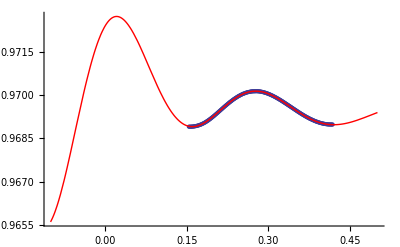

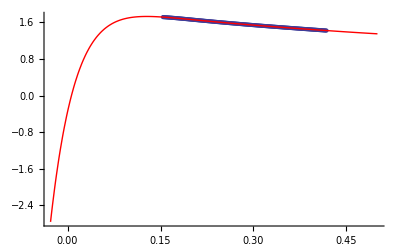

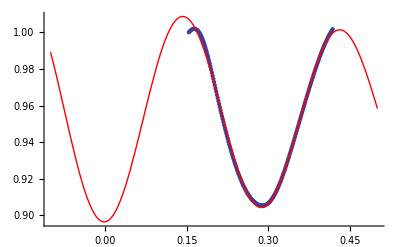

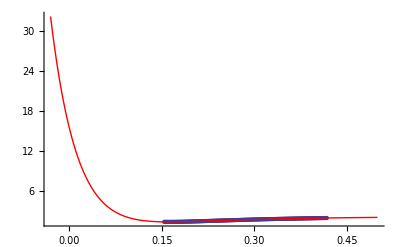

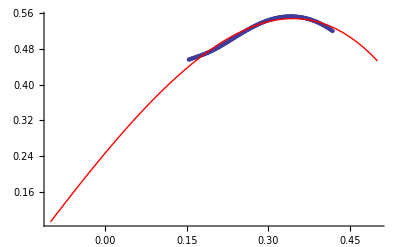

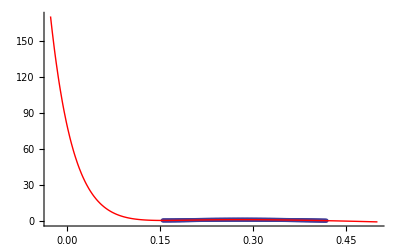

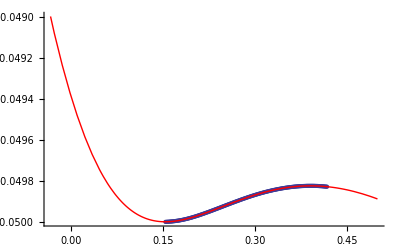

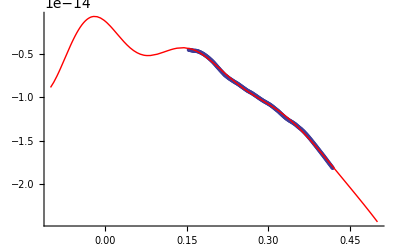

```mathematica
Show[ListPlot[y1],Plot[yModelCWF[1][t]/.y1Fit,{t,-0.1,0.5},PlotStyle->{Red}]]
Show[ListPlot[y2],Plot[yModelCWF[2][t]/.y2Fit,{t,-0.1,0.5},PlotStyle->{Red}]]
Show[ListPlot[y3],Plot[yModelCWF[3][t]/.y3Fit,{t,-0.1,0.5},PlotStyle->{Red}]]
Show[ListPlot[y4],Plot[yModelCWF[4][t]/.y4Fit,{t,-0.1,0.5},PlotStyle->{Red}]]
Show[ListPlot[y5],Plot[yModelCWF[5][t]/.y5Fit,{t,-0.1,0.5},PlotStyle->{Red}]]
Show[ListPlot[y6],Plot[yModelCWF[6][t]/.y6Fit,{t,-0.1,0.5},PlotStyle->{Red}]]
Show[ListPlot[y7],Plot[yModelCWF[7][t]/.y7Fit,{t,-0.1,0.5},PlotStyle->{Red}]]
Show[ListPlot[y8],Plot[yModelCWF[8][t]/.y8Fit,{t,-0.1,0.5},PlotStyle->{Red}]]
Show[ListPlot[y9],Plot[yModelCWF[9][t]/.y9Fit,{t,-0.1,0.5},PlotStyle->{Red}]]
Show[ListPlot[y10],Plot[yModelCWF[10][t]/.y10Fit,{t,-0.1,0.5},PlotStyle->{Red}]]
```

```mathematica
Aout = A/.y1Fit/.y2Fit/.y3Fit/.y4Fit/.y5Fit/.y6Fit/.y7Fit/.y8Fit/.y9Fit/.y10Fit
```

{{0.00202785,23.6052,0.00177989,5.23781,0.000549311,-7.90497,0.969822},{-1.92105,0.00285681,9058.43,18.0247,0.138113,5.28728,1.42756},{-0.0580751,-21.8072,-0.000520896,0.502828,0.327266,-4.62751×10^-10,0.627336},{13.7852,0.00150027,-82633.2,18.1473,-0.150814,6.56813,1.79368},{1.05825,1.14033,-0.858037,-1.52517,0.00384374,1.91814,-0.81541},{76.9221,0.00755466,-98675.4,20.5368,138156.,0.0159536,-138155.},{0.00029093,7.27237,-0.0011716,6.26943,3.31329,0.0341491,-3.36297},{2.1116×10^-15,33.8352,-1.18778×10^-15,6.43082,3.35875×10^-8,0.00228429,-3.35875×10^-8},{4.92074,-0.699737,3.50366,3.40019×10^-7,-4.92085,0.699738,0.000118203},{2.23089,-0.00645726,2348.,22.4922,277.987,0.0119193,-277.984}}

```mathematica
Aout//MatrixForm
```

(0.00202785 | 23.6052 | 0.00177989 | 5.23781 | 0.000549311 | -7.90497 | 0.969822
-1.92105 | 0.00285681 | 9058.43 | 18.0247 | 0.138113 | 5.28728 | 1.42756
-0.0580751 | -21.8072 | -0.000520896 | 0.502828 | 0.327266 | -4.62751×10^-10 | 0.627336
13.7852 | 0.00150027 | -82633.2 | 18.1473 | -0.150814 | 6.56813 | 1.79368
1.05825 | 1.14033 | -0.858037 | -1.52517 | 0.00384374 | 1.91814 | -0.81541
76.9221 | 0.00755466 | -98675.4 | 20.5368 | 138156. | 0.0159536 | -138155.
0.00029093 | 7.27237 | -0.0011716 | 6.26943 | 3.31329 | 0.0341491 | -3.36297
2.1116×10^-15 | 33.8352 | -1.18778×10^-15 | 6.43082 | 3.35875×10^-8 | 0.00228429 | -3.35875×10^-8
4.92074 | -0.699737 | 3.50366 | 3.40019×10^-7 | -4.92085 | 0.699738 | 0.000118203
2.23089 | -0.00645726 | 2348. | 22.4922 | 277.987 | 0.0119193 | -277.984)

```mathematica
SetDirectory[NotebookDirectory[]];
Export["A_fit_single.mat","a_fit"->Aout,"LabeledData"]
```

A_fit_single.mat